Lab 10: Neutron Detectors

J.R. Powers-Luhn
NE550 Thursday 17:30

Utility tools

Raw SPE data

```mathematica
speraw[filename_,directory_]:=Import[directory<>filename]
```

SPE Data length

```mathematica
spedatalength[filename_,directory_]:=ToExpression[StringSplit[Import[directory<>filename][[12]]][[1,2]]]
```

```mathematica
spedatalength["He3 60s 0.5microseconds.Spe",NotebookDirectory[]<>"data/neutron detectors/"]
```

1023

SPE File Importer

```mathematica
spedata[filename_,directory_]:=ToExpression[Import[directory<>filename][[13;;13+spedatalength[filename,directory]]]][[;;,1]]
```

Time of count in SPE file

```mathematica
spetime[filename_,directory_]:=ToExpression[StringSplit[Import[directory<>filename][[10]]][[1,1]]]
```

^3 He neutron detector

1. Properly plot the ^3 He spectra for each shaping time investigated. Put all traces on a single pot, and use the full energy peak that shows up in at least some of the spectra to convert the abscissa to energy (Q-value is 764 keV).

```mathematica
shapingTimes={0.5,1,2,3,6,10}
filenameList=Table["He3 60s "<>ToString[i]<>"microseconds.Spe",{i,shapingTimes}]
```

{0.5,1,2,3,6,10}

{He3 60s 0.5microseconds.Spe,He3 60s 1microseconds.Spe,He3 60s 2microseconds.Spe,He3 60s 3microseconds.Spe,He3 60s 6microseconds.Spe,He3 60s 10microseconds.Spe}

```mathematica
directory=NotebookDirectory[]<>"data/neutron detectors/";
```

```mathematica
qvalue=762(*keV*);
```

```mathematica
peakvalss=Table[Max[i[[60,120]]],{i,Table[spedata[j,directory],{j,filenameList}]}]
```

Part::partd1: Depth of object {0,0,0,0,0,0,0,0,2,42339,85059,41839,22019,12809,8108,5786,4746,4560,4673,5282,5595,5846,6017,6185,6249,6198,6299,5951,5727,5599,5500,5170,5157,5147,5367,5365,5528,5796,5792,6092,6134,5985,6288,6097,6019,5869,5740,5771,5632,5620,«974»} is not sufficient for the given part specification.

Part::partd1: Depth of object {0,0,0,0,0,0,0,0,0,7,7990,4465,2440,1722,1483,1345,1420,1526,1769,2115,2461,2819,2924,3154,3223,3273,3244,3253,3261,3185,3075,3098,3077,2927,3000,2935,2877,2787,2799,2675,2674,2496,2478,2497,2412,2393,2337,2427,2342,2400,«974»} is not sufficient for the given part specification.

Part::partd1: Depth of object {0,0,0,0,0,0,0,0,0,4,8351,5780,3355,2312,1560,1425,1304,1245,1207,1274,1458,1792,2028,2382,2514,2689,2709,2769,2791,2707,2662,2707,2646,2528,2474,2475,2400,2454,2339,2278,2290,2205,2145,2134,2094,2024,2010,2000,1973,1898,«974»} is not sufficient for the given part specification.

General::stop: Further output of Part::partd1 will be suppressed during this calculation.

{{0,0,0,0,0,0,0,0,2,42339,85059,41839,22019,12809,8108,5786,4746,4560,4673,5282,5595,5846,6017,6185,6249,6198,6299,5951,5727,5599,5500,5170,5157,5147,5367,5365,5528,5796,5792,6092,6134,5985,6288,6097,6019,5869,5740,5771,5632,5620,5551,5413,5489,5318,5288,5380,5422,5421,5336,5547,5705,5800,6191,6288,6681,6942,7703,7810,8279,8372,8179,7803,7045,6032,4877,3775,2742,1979,1237,755,445,271,169,123,106,76,76,83,51,63,69,78,70,48,57,82,47,51,31,44,57,48,40,35,26,48,37,39,25,31,32,37,25,29,33,23,28,28,22,20,22,16,17,20,22,16,17,13,15,10,9,10,9,6,10,13,5,1,6,6,6,4,4,3,4,0,7,2,0,1,0,0,1,0,0,1,1,1,0,0,1,1,0,0,1,1,1,0,0,0,1,2,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}⟦60,120⟧,{0,0,0,0,0,0,0,0,0,7,7990,4465,2440,1722,1483,1345,1420,1526,1769,2115,2461,2819,2924,3154,3223,3273,3244,3253,3261,3185,3075,3098,3077,2927,3000,2935,2877,2787,2799,2675,2674,2496,2478,2497,2412,2393,2337,2427,2342,2400,2473,2684,2694,2936,3054,3047,3142,3279,3377,3369,3485,3556,3685,3822,3821,4019,4118,4364,4495,4755,4697,4811,5375,5513,6030,6670,7237,8147,9036,9873,10623,10677,10197,9112,7597,5560,3827,2363,1396,686,335,199,111,77,49,60,64,60,69,70,48,54,61,68,52,47,57,57,58,45,51,54,42,48,43,48,54,38,49,47,38,34,38,33,24,34,29,34,33,37,33,36,31,34,29,27,28,35,18,22,27,30,32,26,25,18,30,22,21,16,24,21,19,17,27,10,17,12,13,16,17,10,19,12,6,14,8,3,3,3,1,1,0,0,1,0,0,1,0,0,0,0,0,1,2,1,1,0,1,1,2,1,1,1,1,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}⟦60,120⟧,{0,0,0,0,0,0,0,0,0,4,8351,5780,3355,2312,1560,1425,1304,1245,1207,1274,1458,1792,2028,2382,2514,2689,2709,2769,2791,2707,2662,2707,2646,2528,2474,2475,2400,2454,2339,2278,2290,2205,2145,2134,2094,2024,2010,2000,1973,1898,1837,1880,1819,1810,1701,1732,1618,1605,1683,1666,1675,1626,1611,1703,1798,1902,2035,2058,2275,2355,2409,2462,2543,2532,2581,2613,2728,2880,3209,3444,3987,4582,5575,6741,8554,10440,12572,14425,15573,16044,14856,12695,10048,6963,4604,2686,1508,882,492,313,212,156,118,92,99,96,100,81,89,94,94,83,90,94,91,99,101,100,95,94,89,97,89,84,83,66,76,71,85,65,75,69,68,58,59,60,65,67,65,53,63,56,67,53,59,56,51,59,55,42,50,47,38,47,36,58,47,52,37,50,48,48,28,34,36,48,35,49,31,45,46,56,48,44,33,50,44,33,28,28,26,25,16,9,5,6,4,2,2,1,3,2,1,1,3,4,2,3,3,1,0,0,1,1,0,3,0,1,0,0,1,0,0,0,4,0,1,0,0,1,0,1,1,1,0,5,0,1,1,0,0,0,1,0,0,0,0,0,0,1,0,1,0,2,0,0,0,0,1,0,0,0,0,1,0,0,0,1,0,1,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}⟦60,120⟧,{0,0,0,0,0,0,0,0,0,0,7150,4946,2896,1986,1645,1395,1228,1144,1105,1099,1265,1504,1836,2112,2356,2673,2597,2595,2606,2512,2553,2499,2511,2448,2427,2361,2338,2247,2292,2165,2157,2022,2024,2011,2036,2062,2093,1895,1800,1801,1753,1859,1669,1688,1714,1727,1636,1607,1513,1566,1555,1492,1458,1558,1503,1503,1572,1677,1884,1985,2097,2154,2274,2329,2299,2411,2400,2397,2439,2485,2586,2722,2987,3454,4128,5456,7268,10017,12918,15409,17697,18253,16727,14090,10537,7151,4581,2665,1590,981,636,426,242,182,167,133,132,110,128,121,127,108,108,122,122,124,117,125,115,145,144,114,135,127,133,130,120,109,100,100,115,101,93,107,100,101,90,83,87,88,97,88,66,73,91,84,74,70,82,56,83,88,72,74,76,55,69,66,66,62,77,76,55,67,61,71,77,66,67,60,70,85,48,70,86,66,62,65,79,68,63,66,58,55,44,44,24,21,17,9,9,4,3,4,2,2,1,3,1,0,2,5,2,2,2,3,1,0,1,2,4,3,3,1,2,1,0,2,2,1,3,3,0,1,0,1,0,0,1,1,3,2,1,1,1,0,1,0,1,0,2,0,1,0,1,0,0,0,0,1,0,0,3,1,0,1,1,1,1,0,0,0,1,1,1,0,1,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}⟦60,120⟧,{0,0,0,0,0,0,0,0,0,41,11082,5015,2483,1677,1500,1349,1228,1070,937,886,930,1098,1321,1724,1987,2159,2423,2363,2372,2403,2403,2426,2326,2332,2309,2292,2251,2281,2202,2164,2059,2113,2055,2065,2041,1961,1877,1810,1879,1863,1730,1739,1702,1672,1674,1710,1673,1592,1537,1511,1573,1441,1457,1479,1455,1396,1322,1364,1348,1481,1425,1553,1736,1815,1947,2088,2032,2171,2159,2163,2163,2287,2261,2415,2265,2406,2523,2738,3013,3585,5020,7232,10795,14987,18945,20329,19478,15796,11578,7799,5605,4148,3242,2404,1586,1025,632,376,301,236,233,228,185,233,227,200,214,214,226,231,232,197,239,218,229,206,251,233,247,235,243,224,239,227,204,237,208,238,202,201,184,194,169,179,193,180,164,170,175,134,181,141,141,139,155,154,160,137,132,125,132,153,141,121,142,154,135,138,147,144,145,141,146,130,151,136,150,114,145,134,125,139,110,120,133,120,145,149,157,162,153,127,129,104,78,71,37,39,33,16,22,14,13,7,13,5,7,3,7,8,6,5,4,6,6,10,8,4,3,6,11,8,10,7,3,10,8,2,3,4,4,2,11,1,4,2,3,3,5,3,2,3,5,6,4,1,5,6,6,3,1,5,4,1,4,2,2,1,4,4,1,0,2,2,2,3,2,6,0,1,3,1,3,2,1,1,2,0,2,2,0,0,4,0,1,2,1,2,0,1,1,1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,2,0,1,0,1,0,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}⟦60,120⟧,{0,0,0,0,0,0,0,0,0,8,1351,1363,1427,1464,1393,1218,1040,887,740,642,683,744,1228,1659,2030,2164,2262,2229,2225,2337,2202,2375,2288,2308,2246,2210,2141,2162,1936,1964,2003,1968,1912,1973,1768,1882,1832,1822,1758,1791,1732,1685,1710,1646,1612,1591,1541,1537,1506,1533,1495,1479,1361,1426,1409,1357,1369,1363,1279,1342,1335,1301,1384,1543,1645,1844,1929,1928,2076,2105,2077,2158,2021,2105,2148,2168,2271,2286,2504,2618,2768,3208,4110,6089,9445,14158,19061,21627,21206,17008,11496,7245,4895,3661,2728,1859,1155,660,429,400,362,339,315,333,334,348,334,302,324,325,340,297,350,356,344,336,335,370,325,363,362,373,355,368,347,383,329,316,352,326,312,296,329,308,275,259,249,266,237,278,226,269,247,259,269,250,226,217,252,224,218,246,220,221,197,227,225,228,223,215,229,252,213,216,208,235,193,207,214,218,200,204,213,214,227,206,207,213,225,212,231,228,259,257,253,250,224,173,136,107,86,76,66,47,30,29,28,27,24,23,27,16,22,23,27,12,23,22,17,22,17,20,15,14,19,13,15,19,18,17,9,14,21,11,14,17,11,17,10,11,11,9,11,7,12,8,9,7,11,10,4,7,10,11,9,5,11,3,8,6,6,9,9,8,8,5,4,4,2,7,5,7,4,5,4,8,3,10,2,4,3,5,5,4,1,3,3,3,6,7,3,3,1,1,4,1,3,2,0,0,0,0,1,2,0,1,0,0,1,1,0,0,1,0,1,1,1,0,0,0,1,0,0,0,0,2,0,0,1,0,2,0,0,0,1,0,0,0,1,0,0,0,0,2,0,0,0,1,0,3,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}⟦60,120⟧}

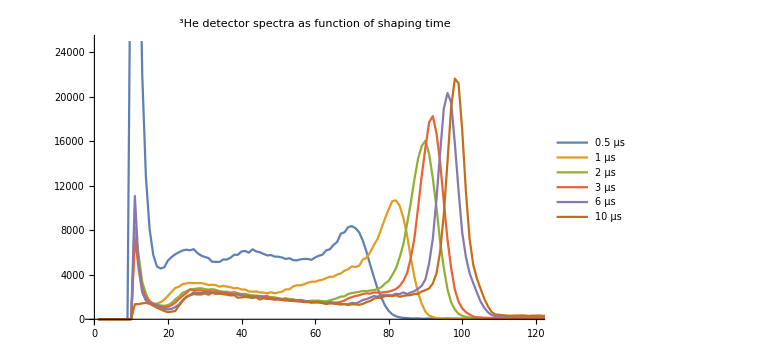

```mathematica
ListPlot[Table[spedata[i,directory],{i,filenameList}],PlotRange->{{0,120},{0,25000}},PlotLabel->Style["^3He detector spectra as function of shaping time",24],ImageSize->Large,Joined->True,PlotLegends->Placed[Table[ToString[i]<>" μs",{i,shapingTimes}],{0.5,0.75}]]
```

2. From the plot, and in a text-style cell, discuss what shaping time is needed to obtain a quality spectrum from the ^3 He detector (i.e., full energy peak with wall effects).

3. In another text-style cell, comment on the reason behind the required shaping time. That is, why is the peaking time found necessary required? What is it a function of?

4. If we wish to only count neutron events, identify which energy value on the abscissa would be chosen to discriminate counts from the very low energy region of the spectrum. Put your answer in a text-style cell.

BF_3 neutron detector

1. Properly plot the BF_3 spectra for each shaping time investigated. Put all traces on a single plot, and use the full energy peak that shows up in at least some of the spectra to convert the abscissa to energy (Q-value is 2.79 MeV, but the ^7 Li product only goes to the ground state 6% of the time.

2. From the plot, and in a text-style cell, discuss what shaping time is needed to obtain a quality spectrum from the BF_3 detector (i.e., full energy peak with wall effects).

3. In another text-style cell, comment on the reason behind the required shaping time. That is, why is the peaking time found necessary required? What is it a function of?

4. If we wish to only count neutron events, identify which energy value on the abscissa would be chosen to discriminate counts from the very low energy region of the spectrum. Put your answer in a text-style cell.

Boron loaded organic scintillator

1. Plot the two spectra on the sample plot (properly formatted) when the Na-22 source is and is not present near the boron loaded organic scintillator.

2. Using the drawing tools, identify the thermal neutron response in both spectra (again, this is the plot in (1)) and the Na-22 contribution observed in one of the two spectra.

3. In a text-style cell, comment on whether the Na-22 source interferes with counting thermal neutrons with this organic scintillator. Specifically comment on the threshold (i.e., value on the abscissa) you would choose to discriminate between gamma-rays and neutrons.

EJ-299 Pulse Shape Discrimination Plastic

1. Plot the two spectra on the sample plot (properly formatted) when the Na-22 source is and is not present near the EJ-299 detector.

2. Using the drawing tools, identify the fast neutron response in both spectra (again, this is the plot in (1)) and the Na-22 contribution observed in one of the two spectra.

3. In a text-style cell, comment on whether the Na-22 source interferes with counting fast neutrons with this organic scintillator. Specifically comment on the threshold (i.e., value on the abscissa) you would choose to discriminate between gamma-rays and neutrons, if any is appropriate at all.

4. Import the 2D PSD plot collected using the V1720 digitizer with PSD capability. Looking at this plot, qualitatively discuss, in a text-style cell, how well EJ-299 discriminates signals from gamma rays and neutrons. Pay particular attention to the lower integrated pulse region (low end of abscissa). For the abscissa value where a clear separation is observed between gamma rays and neutrons, theorize if this abscissa value is superior to just collecting a pulse height spectrum and choosing some threshold, if any (plot from (1) and discussion in (3)).